# Year 10 Curriculum

# Mathematica Bound-Reference

## Authored by gptreliance

Topic01

Linear Relations and Equations

## Performing Basic Operations

Use + for addition

Use - for subtraction

Use * for multiplication

Use / for division

Press Ctrl + / for a fraction (x/y)

Use ^ for powers, or Ctrl + 6

Use /. to substitute

Usage: equation /. variable => number

```mathematica
2a+5/.a->3
```

11

## Simplifying Expressions

Typing an expression and executing it (Shift + Enter) will automatically simplify things:

```mathematica
4a+3b-12b+4a*b
```

4 a-9 b+4 a b

Simplify[] or FullSimplify[] can also be used

```mathematica
Simplify[2x+4-3(x+1)]
```

1-x

## Factorising and Expanding

Expand expands the following

```mathematica
Expand[(x+1) (2x+1) (3x+1)]
```

1+6 x+11 x^2+6 x^3

Factor factorises the following:

```mathematica
Factor[1+6x+11 x^2+6 x^3]
```

(1+x) (1+2 x) (1+3 x)

Fancy shortcuts used: Ctrl+6 (Hat/Exponent key) for exponent (x^6)

## Solving Equations

Always use a double equals sign (‘==’, like python) or you permanently DEFINE the variable x

Usage: Solve[expression == expression2, unknown]

```mathematica
Solve[7x-1==2x+4,x]
```

{{x→1}}

## Solving Inequations

You must use Reduce[] to solve inequalities, Solve[] will not work

Usage: Reduce[expression (>, <, >= or <=) expression2, unknown]

```mathematica
Reduce[5x-1>x+4,x]
```

x>5/4

Using >= or <= (python style!) automatically simplifies to the proper symbol.

```mathematica
Reduce[20x-80>=50x-130,x]
```

x≤5/3

## Working with Fractions

This combines fractions together by putting fractional expressions over a common denominator

Usage: Together[equation of the fraction]

```mathematica
Together[(2x-1)/(x+4)^2-1/(x+4)]
```

(-5+x)/(4+x)^2

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction (x/y), Ctrl+6 (Hat/Exponent key) for exponent (x^6)

## Troubleshooting Section (check at end of every lesson)

Remember to use a double equals (==) sign

Try to use Clear or ClearAll to remove accidental variable assigns

```mathematica
Clear[x]
```

Usage: Clear[some_variable_you_want_cleared], clears definitions

```mathematica
ClearAll[x,y,z]
```

Usage: ClearAll[some_variables_you_want_cleared], clears all associations, messages, values and associations

Remember, Solve command needs to know which variable needs to be found

e.g. Solve[50x-10==30x-20, x] <- That “x” needs to be stated

Variables are blue, commands are black and need to be in title case (e.g. Solve[])

Topic 02

Linear Graphs and Functions

## Solving Simultaneous Equations

If there are multiple things going into a single parameter, use curly braces to fit them.

e.g. When solving two or more equations, the equations must be in curly braces, separated by a comma.

Remember to use double equals “==” similar to other programming languages.

```mathematica
Solve[{y==2x-1,y==3-x},{x,y}]
```

{{x→4/3,y→5/3}}

Usage: Solve[{equation_a, equation_b}, {variable_to_be_found_a, variable_to_be_found_b}]

If a variable has already been defined, don’t forget to use ClearAll.

```mathematica
ClearAll[x,y]
```

## Plotting Graphs

Plot has many parameters that can be set, depending on different use cases.

### Simple Plot

This first one is simple, equation* first, domain (x) second.

The equation does not need a y, it is only an expression.

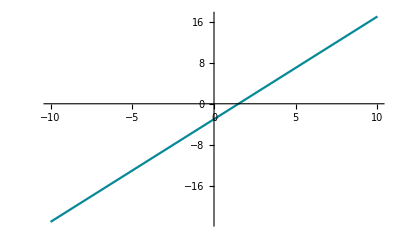

```mathematica
Plot[2x-3,{x,-10,10}]
```

Usage: Plot[equation, {domain_parameter}]

### Plotting with range (y) parameter

This second one adds a plotting range (y) to the equation. It is preceded by PlotRange ->

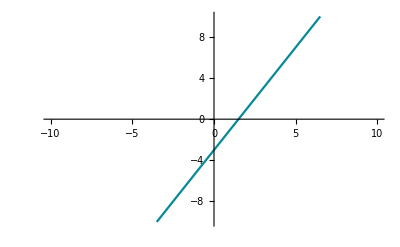

```mathematica
Plot[2x-3,{x,-10,10},PlotRange->{-10,10}]
```

Usage: Plot[equation, {domain_parameter}, PlotRange->{range_parameter}]

#### PlotRange Shortcut

You can replace “PlotRange -> {-10, 10}” with “PlotRange -> 10”, it automatically sets the range to 10 both ways of the y-axis.

```mathematica
Plot[2x-3,{x,-10,10},PlotRange->{-10,10}]
```

-Graphics-

Usage: Plot[equation, {domain_parameter}, PlotRange->{range_parameter}]

### Plotting with Multiple Equations

This one throws a second equation into the mix.

Because it involves multiple elements in a single parameter, the equations (expressions rather) are placed in curly braces {}

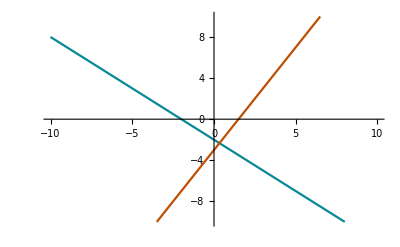

```mathematica
Plot[{-x-2,2x-3},{x,-10,10},PlotRange->{-10,10}]
```

Usage: Plot[{equation_a, equation_b}, {domain_parameter}, PlotRange->{range_parameter}]

### Adding Legends

You can add legends to the graph to know which graph belongs to which equation. This uses the PlotLegends parameter. The “Expressions” tells Mathematica to write the expression beside the legend.

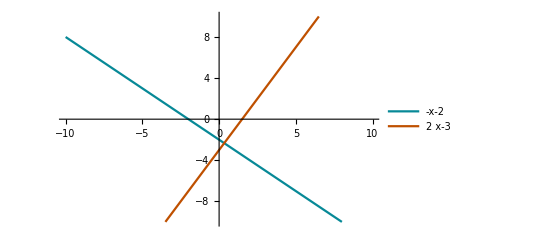

```mathematica
Plot[{-x-2,2x-3},{x,-10,10},PlotRange->{-10,10},PlotLegends->"Expressions"]
```

Usage: Plot[{equation_a, equation_b}, {domain_parameter}, PlotRange->{range_parameter}]